```mathematica
triples=Import[NotebookDirectory[]<>"coprime_triples.csv"];
pairs=Import[NotebookDirectory[]<>"coprime_pairs.csv"];
```

```mathematica
show[m_,p_,K_:"K"]:=Module[{r,pos,coef},r=p["r"];
pos=p["pos"];coef=p["coef"];
Do[Print[Subscript[Superscript["Ψ",Row[{m,"+",K}]],r[[i]]],"=",Sum[Subscript["ψ",m,pos[[i,j]]]coef[[i,j]],{j,1,Length[pos[[i]]]}]],{i,1,Length[r]}];]
```

```mathematica
showtriple[triple_]:=Module[{m,filename,p},
m=Times@@triple;filename=NotebookDirectory[]<>"data/seifert/projections/"<>StringRiffle[triple,"_"]<>".json";p=Import[filename,"RawJSON"];
show[m,p];]
showpair[pair_]:=Module[{m,ab,filename,p},
m=Times@@pair;
ab={"a","b"};Do[filename=NotebookDirectory[]<>"data/seifert/projections/"<>StringRiffle[pair,"_"]<>ab[[i]]<>".json";p[i]=Import[filename,"RawJSON"],{i,1,2}];
Do[show[m,p[i],pair[[i]]],{i,1,2}];]
```

Now look at other two quantities, α_r:=(Σ^4)_(i=1)c_i(m-r_i) and Σ_i c_i which depend only on the projections, and see how the accumulative number of these two variable changes.

```mathematica
FileExistsQ[NotebookDirectory[]<>"data/seifert/projections/"<>StringRiffle[triples[[500]],"_"]<>".json"]
```

True

```mathematica
p=Import[NotebookDirectory[]<>"data/seifert/projections/"<>StringRiffle[triples[[300]],"_"]<>".json","RawJSON"];
```

```mathematica
p["pos"][[1]]
p["coef"][[1]]
```

{1,139,321,461,1149,1289,1471,1609}

{1,1,1,-1,1,-1,-1,-1}

```mathematica
Total[{1,1,1,-1,1,-1,-1,-1}[[;;4]]]
```

2

```mathematica
p["r"]//Length
```

132

```mathematica
FileExistsQ[NotebookDirectory[]<>"data/seifert/projections/"<>StringRiffle[triples[[600]],"_"]<>".json"]
```

False

```mathematica
trc={};
alphar={};
mlist={};
rlist={};
cutoff=500;
Do[
triple=triples[[i]];
m=Times@@triple;
filename=NotebookDirectory[]<>"data/seifert/projections/"<>StringRiffle[triple,"_"]<>".json";p=Import[filename,"RawJSON"];
coef=p["coef"];
pos=p["pos"];
Do[
AppendTo[trc,Total[coef[[j,;;4]]]];
AppendTo[alphar,Sum[coef[[j,k]](m-pos[[j,k]]),{k,1,4}]];
AppendTo[mlist,m];
AppendTo[rlist,pos[[j,1]]];
,{j,1,Length[coef]}]
,{i,1,400}]
```

```mathematica
alphar//Length
```

30295

```mathematica
Sum[(Times@@(triples[[i]]-1)/4),{i,1,601}]
```

62020

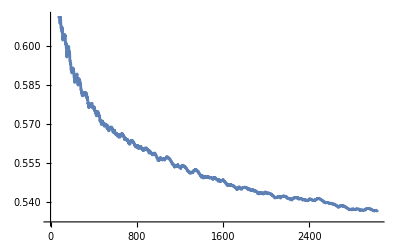

```mathematica
ListLinePlot[Table[Total[Unitize[alphar[[;;n]]]]/n,{n,1,30295,10}]]
```

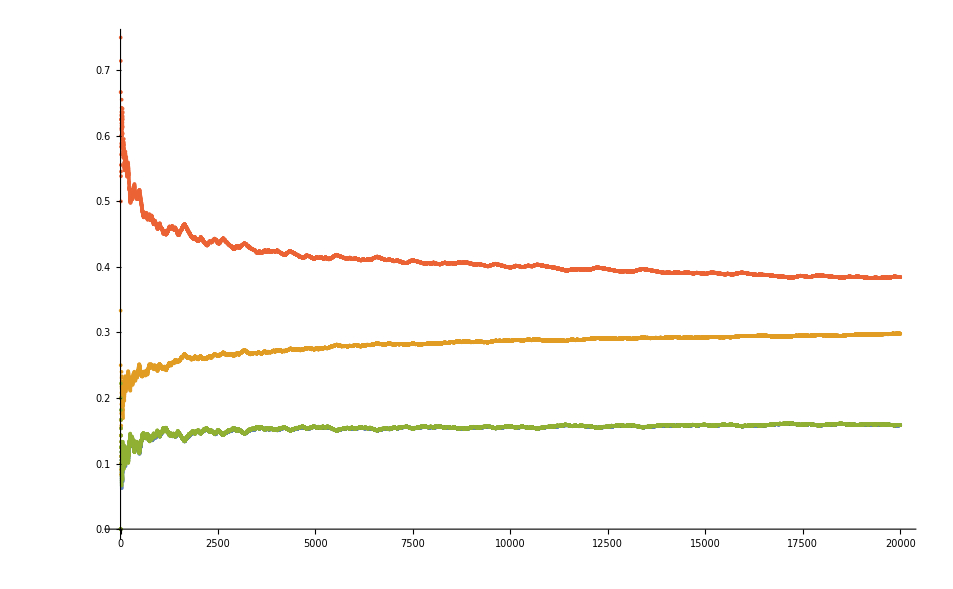

```mathematica
cutoff=20000;
ListPlot[Table[Table[Count[trc[[;;n]],2parameter-4]/n,{n,1,cutoff}],{parameter,1,4}]]
```

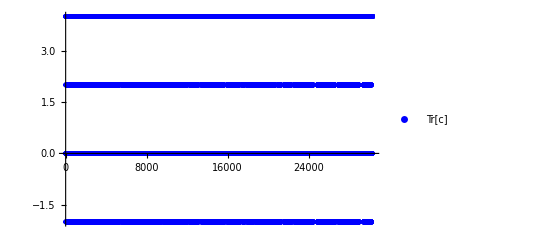

```mathematica
Show[(*ListPlot[Unitize[alphar[[;;100]]],PlotStyle->Red,PlotMarkers->{"●",4},PlotLegends->{Subscript["α","r"]}],*)ListPlot[trc,PlotStyle->Blue,PlotMarkers->{"●",5},PlotLegends->{"Tr[c]"}]]
```

```mathematica
showtriple[triples[[2]]]
```

(Ψ^(42+K))_1=ψ_(42,1)-ψ_(42,13)-ψ_(42,29)+ψ_(42,41)-ψ_(42,43)+ψ_(42,55)+ψ_(42,71)-ψ_(42,83)

(Ψ^(42+K))_5=ψ_(42,5)+ψ_(42,19)+ψ_(42,23)+ψ_(42,37)-ψ_(42,47)-ψ_(42,61)-ψ_(42,65)-ψ_(42,79)

(Ψ^(42+K))_11=ψ_(42,11)+ψ_(42,17)+ψ_(42,25)+ψ_(42,31)-ψ_(42,53)-ψ_(42,59)-ψ_(42,67)-ψ_(42,73)

```mathematica
showpair[pairs[[3]]]
```

(Ψ^(12+3))_1=ψ_(12,1)-ψ_(12,7)+ψ_(12,17)-ψ_(12,23)

(Ψ^(12+3))_2=ψ_(12,2)+ψ_(12,10)-ψ_(12,14)-ψ_(12,22)

(Ψ^(12+3))_3=2 ψ_(12,3)-2 ψ_(12,21)

(Ψ^(12+3))_5=ψ_(12,5)-ψ_(12,11)+ψ_(12,13)-ψ_(12,19)

(Ψ^(12+3))_6=2 ψ_(12,6)-2 ψ_(12,18)

(Ψ^(12+3))_9=2 ψ_(12,9)-2 ψ_(12,15)

(Ψ^(12+4))_1=ψ_(12,1)+ψ_(12,7)-ψ_(12,17)-ψ_(12,23)

(Ψ^(12+4))_2=ψ_(12,2)-ψ_(12,10)+ψ_(12,14)-ψ_(12,22)

(Ψ^(12+4))_4=2 ψ_(12,4)-2 ψ_(12,20)

(Ψ^(12+4))_5=ψ_(12,5)+ψ_(12,11)-ψ_(12,13)-ψ_(12,19)

(Ψ^(12+4))_8=2 ψ_(12,8)-2 ψ_(12,16)

```mathematica
total=0;
Do[pair=pairs[[j]];
Do[filename=NotebookDirectory[]<>"data/seifert/projections/"<>StringRiffle[pair,"_"]<>ab[[i]]<>".json";p[i]=Import[filename,"RawJSON"],{i,1,2}];
total+=Sum[Length[p[i]["r"]],{i,1,2}],{j,1,500}
]
```

```mathematica
Do[
filename=NotebookDirectory[]<>"data/theta/"<>ToString[m]<>"_"<>ToString[r]<>".json";If[!FileExistsQ[filename],psimr=psi[m,r,50];
Export[filename,<|"pref"->psimr[[1]],"signs"->psimr[[2]],"expo"->psimr[[3]]|>]],{m,1, 150},{r,0,m-1}]
```

```mathematica
expo={};mr={};
Do[filename=NotebookDirectory[]<>"data/theta/"<>ToString[m]<>"_"<>ToString[r]<>".json";
s=Import[filename,"RawJSON"];
AppendTo[expo,Take[s["signs"],20]*Take[s["expo"],20]];AppendTo[mr,{m,r}],{m,1,150},{r,0,m-1}]
```

```mathematica
mr={};
Do[triple=triples[[i]];
m=Times@@triple;filename=NotebookDirectory[]<>"data/seifert/projections/"<>StringRiffle[triple,"_"]<>".json";rs=Import[filename,"RawJSON"]["r"];Do[AppendTo[mr,{m,rs[[j]]}],{j,1,Length[rs]}],{i,1,601}]
```

```mathematica
expos={};
Do[{m,r}=mr[[i]];filename=NotebookDirectory[]<>"data/theta/"<>ToString[m]<>"_"<>ToString[r]<>".json";
s=Import[filename,"RawJSON"];
AppendTo[expos,Take[s["signs"],20]*Take[s["expo"],20]],{i,1,Length[mr]}]
```

```mathematica
Export[NotebookDirectory[]<>"psimr_new_x.csv",expos]
```

/Users/lithium/Downloads/BPS-spectra/psimr_new_x.csv

```mathematica
Export[NotebookDirectory[]<>"psimr_new_y.csv",mr]
```

/Users/lithium/Downloads/BPS-spectra/psimr_new_y.csv

```mathematica
expos//Dimensions
```

{10010,20}

```mathematica
triple=triples[[1]];
m=Times@@triple;filename=NotebookDirectory[]<>"data/seifert/projections/"<>StringRiffle[triple,"_"]<>".json";rs=Import[filename,"RawJSON"]["r"]
```

{1,7}

```mathematica
Sum[Times@@(triples[[i]]-1)/4,{i,1,601}]
```

62020

```mathematica
Do[triple=triples[[i]];
filename=NotebookDirectory[]<>"data/seifert/projections/"<>StringRiffle[triple,"_"]<>".json";
If[!FileExistsQ[filename],
m=Times@@triple;
p=proj[m,ktriple[triple]];
data=flatproj[p];
r=data[[1]];
Export[filename,<|"r"->data[[1]],"pos"->data[[2]],"coef"->data[[3]]|>]],{i,500,601}]
```

$Aborted

```mathematica
filename
```

/Users/lithium/Downloads/BPS-spectra/data/seifert/projections/2_13_47.json

```mathematica
triple
```

{2,13,47}

```mathematica
hyper={};
Do[h=Import[NotebookDirectory[]<>"/data/hyperbolic/r"<>ToString[r]<>".csv"][[All,;;20]]//Flatten;
AppendTo[hyper,h];
,{r,2,20000}]
```

```mathematica
Export[NotebookDirectory[]<>"/data/hyperall.csv",hyper]
```

/Users/lithium/Downloads/BPS-spectra//data/hyperall.csv

```mathematica
hyper//Dimensions
```

{19999,40}

```mathematica
hypery=Table[i,{i,2,20000}];
Export[NotebookDirectory[]<>"/data/hyper_y.csv",hypery]
```

/Users/lithium/Downloads/BPS-spectra//data/hyper_y.csv

```mathematica
hypery//Dimensions
```

{19999}